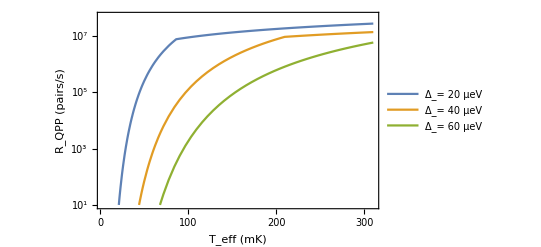

```mathematica
(* Panel C of Figure 3 of the main text *)
(* plot of rate of quasiparticle pair excitation versus gap at a fixed TLF effective temperature *)
(* this plot allows for the effects of high attempt frequency for a TLF that is thermally excited over an energy barrier *)

(* all calculations are done in units of gigahertz and microns *)
(* conversions are 1 μeV = 0.0116 K, 1 μeV = 0.2418 GHz  *)
ClearAll["Global`*"];

mykT=.;
mykTinmK=.;
myDelta=.;
myDeltainmicrovolts=.;
myGamma0=.;

length=3. ;        (* length = 3 microns *)
deltamu=0.138;(* deltamu is in GHz *)
(* prefactor=(length/16)*(deltamu)^2/vFermi this is prefactor in units of ns *)
(* let's write prefactor in Hz: *)

(* Fermi velocity is gap-dependent *)
(* the expression below is appropriate when mu=0 and is derived by assuming that the superconducting coherence length is 0.25 microns.  In any case, the dependence on Fermi velocity is rather weak and does not affect the qualitative conclusions  *)
vFermi[myDelta_]:=1.25*myDelta; (* vFermi = (1.25)(gap in GHz) microns/ns *)

(*prefactor of the pair excitation rate is a function of temperature and also of myDelta (in GHz).  The 10^9 in the prefactor is there to get the rate to come out in units of pairs/s instead of pairs/ns.  *)
prefactor[mykT_?NumericQ,myDelta_?NumericQ]:=(10^9*(length/16)*(deltamu)^2/vFermi[myDelta])*(mykT/1.04);


(* Note that the prefactor is proportional to T according to Dutta and Horn because density of epsilons (TLF asymmetries) is uniform and all the TLFs with epsilon \lessim kT are active.  We will assume that Microsoft experiment was done at T_eff = 0.05 K, so the prefactor has a factor of (T_eff/0.05 K) = (T_eff/1.04) when converted to GHz. *)

(* function that calculates the pair excitation rate *)
(* The rate is based on the fact that the total rate from all the TLFs is dominated by the contribution of the dominant transition rate Γ.  This rate grows with the transition rate Γ until Γ exceeds 2Δ, and then is suppressed exponentially with a factor of Exp[-(Γ/2Δ)].  The rate is also suppressed exponentially if 2Δ/Subscript[k, B] Subscript[T, eff] is large by the factor Exp[-(2Δ/Subscript[k, B] Subscript[T, eff])].   *)

(* This program also incorporates the effects of a large attempt frequency Subscript[Γ, 0].  For classical activation over the barrier, energy is available to excite a quasiparticle pair if 2*myDelta/mykT is less than Log[myGamma0/myGamma]. The Log term is just Subscript[E, B]/Subscript[k, B] Subscript[T, eff], where Subscript[E, B] is the energy barrier that is overcome when the TLF makes a transition.
This term does not enter if myGamma0 is equal to myGamma. *)

rate[myGamma_?NumericQ,myDelta_?NumericQ,mykT_?NumericQ,myGamma0_?NumericQ]:=prefactor[mykT,myDelta]*(myGamma/myDelta)*Exp[(-Max[2*myDelta/mykT-Log[myGamma0/myGamma],0]+myGamma/(2*myDelta))];

maxRate[myDelta_?NumericQ,mykT_?NumericQ,myGamma0_?NumericQ]:=NMaxValue[{rate[myGamma,myDelta,mykT,myGamma0],0<myGamma<2*myDelta},myGamma];

mykT=mykTinmK*0.0284; (* converts mK to GHz *)
myDelta=myDeltainmicrovolts*0.2418;  (* converts microeV to GHz *)(* will plot rate versus myDelta at different effective temperatures *)
(* *)
mykT=mykTinmK*0.0284; (* converts mK to GHz *)
myDelta=myDeltainmicrovolts*0.2418;  (* converts microeV to GHz *)

(* now plot rate versus T_eff for different Deltas *)
(* the function includes mygamma0, which is the attempt frequency, which is a relevant parameter for a specific model in which the TLFs are activated over a barrier.  The attempt frequency is not an issue when myGamma0 is equal to the effective temperature (which for  *)

LogPlot[{maxRate[myDelta,mykT,myGamma0]/.{myGamma0->500,myDeltainmicrovolts->20},maxRate[myDelta,mykT,myGamma0]/.{myGamma0->500,myDeltainmicrovolts->40} ,
maxRate[myDelta,mykT,myGamma0]/.{myGamma0->500,myDeltainmicrovolts->60}
},
{mykTinmK,3,310},
Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->12,FontFamily->"Helvetica"},FrameLabel->{"T_eff (mK)","R_QPP (pairs/s)",None,None},
PlotRange->{{3,310},{10,5*10^7}},
FrameTicks->{{{{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"},{10^5,"10^5"},{10^6,"10^6"},{10^7,"10^7"}},None},{{0,50,100,150,200,250,300},None}},
PlotLegends->Placed[{"\!\(\*SubscriptBox[\(Δ\), \( \)]\)= 20 μeV","\!\(\*SubscriptBox[\(Δ\), \( \)]\)= 40 μeV","\!\(\*SubscriptBox[\(Δ\), \( \)]\)= 60 μeV","\!\(\*SubscriptBox[\(Δ\), \( \)]\)= 60 μeV"},(* {0.79,0.69} *)Right],
ImageSize->{Automatic,200}
]
myDeltainmicrovolts=.;
```